```mathematica
X={1,1,0,0,0,1,1,2,1,1,1,0,2,2,4,3,2,0,2,2,2,2,3,1,0,2,0,5,3,6,2,1,2,1,8,11,5,8,12,15,22,48,50,73,92,108,113,149,123,97,75,34,6};
n=Length[X]
```

53

-9.27953+0.303433 t

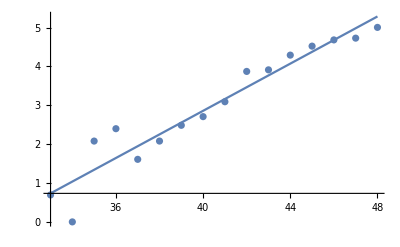

0.288207

{{a→0.22662}}

0.226244

-5.82101

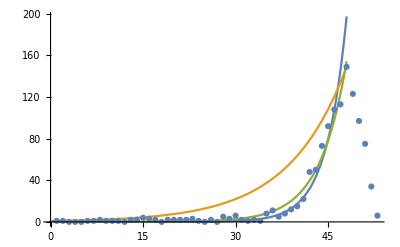

```mathematica
Fit[Table[{t,Log[X[[t]]]},{t,33,48}],{1,t},t]
Show[Plot[%,{t,33,48}],ListPlot[Table[{t,Log[X[[t]]]},{t,33,48}]],PlotRange->All]
a=(Mean[Table[Log[X[[t]]] t,{t,33,49}]]-41Mean[Table[Log[X[[t]]],{t,33,49}]])/(Mean[Table[t^2,{t,33,49}]]-41^2)//N
Clear[a];NSolve[Sum[X[[t]] Exp[a*t] t,{t,33,48}]/Sum[Exp[2a*t] t,{t,33,48}]== Sum[X[[t]] Exp[a*t] ,{t,33,48}]/Sum[ Exp[2a*t],{t,33,48}],a,Reals]
Clear[a];a=a/.Flatten[NSolve[ Sum[X[[t]] Exp[a*t] t,{t,48}]/Sum[Exp[2a*t] t,{t,48}]== Sum[X[[t]] Exp[a*t] ,{t,48}]/Sum[ Exp[2a*t],{t,48}],a,Reals]]
b=Log[Sum[X[[t]] Exp[a*t] ,{t,48}]/Sum[ Exp[2a*t],{t,48}]]
Show[Plot[{Exp[%%%%%%],149^((t-1)/47),Exp[a*t+b]},{t,0,48},PlotRange->All],ListPlot[Table[{t,X[[t]]},{t,n }]],PlotRange->All]
```